# Rearranging Expressions

The functions defined in the PeterBurbery`BasicHypergeometricFunctions` context provide support for placing the q in front.

This loads the package:

```mathematica
<<PeterBurbery`BasicHypergeometricFunctions`
```

## Put Q in the front

The built-in function PositionQInFrontOfList puts q in front of a list. The function works by using UnsortedComplement.

```mathematica
PositionQInFrontOfList[{b,c,d,q,f,q}]
```

{q,q,b,c,d,f}

## Rearranging

This is the expression tree of a a b s a s q s d s d:

```mathematica
exampleInput=a b s a s q s d s d
```

a^2 b d^2 q s^4

```mathematica
ExpressionTree[exampleInput]
```

-Graphics-

We want to put q in the front. We need to verify q is in the expression first:

```mathematica
Position[exampleInput,q]
```

{{4}}

An expression without q would have a different output.

```mathematica
expressionWithNoQ=b d
```

b d

```mathematica
Position[expressionWithNoQ,q]
```

{}

The q could be raised to a power:

```mathematica
qraisedtothepower=b d q^2 d b
```

b^2 d^2 q^2

```mathematica
Position[qraisedtothepower,q]
```

{{3,1}}

Let's look at these three examples from the perspective of Cases:

```mathematica
Cases[exampleInput,q]
```

{q}

```mathematica
Cases[expressionWithNoQ,q]
```

{}

```mathematica
Cases[qraisedtothepower,q]
```

{}

The last example should have something, but q is on a higher level. Let's look at the expression tree.

```mathematica
ExpressionTree[qraisedtothepower]
```

-Graphics-

```mathematica
TreeLevel[ExpressionTree[qraisedtothepower],1]
```

{-Graphics-,-Graphics-,-Graphics-}

q is on the second level:

```mathematica
TreeLevel[ExpressionTree[qraisedtothepower],2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We might want just level 2 and not the subtrees. We can specify this:

```mathematica
TreeLevel[ExpressionTree[qraisedtothepower],{2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

q is in the leaves:

```mathematica
TreeLeaves[ExpressionTree[qraisedtothepower]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We can also use -1 level specification:

```mathematica
TreeLevel[ExpressionTree[qraisedtothepower],{-1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Another way to get q is with TreeLeafQ:

```mathematica
TreeSelect[ExpressionTree[qraisedtothepower],TreeLeafQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We can get the data with TreeData:

```mathematica
TreeData/@TreeSelect[ExpressionTree[qraisedtothepower],TreeLeafQ]
```

{b,2,d,2,q,2}

If q is in the expression, then q will be in this list. Otherwise it will not be.

```mathematica
TreeData/@TreeSelect[ExpressionTree[expressionWithNoQ],TreeLeafQ]
```

{b,d}

```mathematica
MemberQ[TreeData/@TreeSelect[ExpressionTree[expressionWithNoQ],TreeLeafQ],q]
```

False

Make a function to test if q is in an expression:

```mathematica
myQWithinExpressionQ[input_]:=MemberQ[TreeData/@TreeSelect[ExpressionTree[input],TreeLeafQ],q]
```

Test the function:

```mathematica
myQWithinExpressionQ[expressionWithNoQ]
```

False

Test all the examples with the SameTest QInExpressionQ[#1] == #2.

```mathematica
TestReport[MapThread[TestCreate[#1,#2,TestID->Automatic]&,{{expressionWithNoQ,qraisedtothepower,exampleInput},{False,True,True}}],SameTest->(myQWithinExpressionQ[#1]==#2&)]
```

TestReportObject[…]

There is now the function QWithinExpressionQ built in.

```mathematica
QWithinExpressionQ/@{expressionWithNoQ,qraisedtothepower,exampleInput}
```

{False,True,True}

Let's look at two examples and try to find some similarities:

```mathematica
Multicolumn[{ExpressionTree[exampleInput],ExpressionTree[qraisedtothepower]}]
```

-Graphics- | -Graphics-

```mathematica
TreeSelect[ExpressionTree[exampleInput],TreeData[#]==Times&&MemberQ[TreeData/@TreeLeaves[#],q]&]
```

{-Graphics-}

Let's add Times but without a q:

```mathematica
complicatedexpression=exampleInput/(expressionWithNoQ+qraisedtothepower)
```

(a^2 b d^2 q s^4)/(b d+b^2 d^2 q^2)

```mathematica
ExpressionTree[complicatedexpression]
```

-Graphics-

Which Times contain a q?

```mathematica
TreeSelect[ExpressionTree[complicatedexpression],TreeData[#]==Times&&MemberQ[TreeData/@TreeLeaves[#],q]&,Infinity]
```

{-Graphics-,-Graphics-}

```mathematica
TreeSelect[ExpressionTree[complicatedexpression],TreeData[#]==Times&,Infinity]
```

{-Graphics-,-Graphics-,-Graphics-}

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

## Examples

### Example 1

Consider the input q. q is already in front. We can use AtomQ to just return the output.

This

```mathematica
RearrangeFunction[i_?AtomQ]:=i
```

It works with q:

```mathematica
RearrangeFunction[q]
```

q

It works with other symbols:

```mathematica
RearrangeFunction[r]
```

r

### Example 2

The next example is ((b c d z)/(q a))^2.

```mathematica
example2=((b c d z)/(q a))^2
```

(b^2 c^2 d^2 z^2)/(a^2 q^2)

We need

```mathematica
output2=Inactivate[(b^2 c^2 d^2 z^2)/(q^2 a^2),Times]
```

b^2×c^2×d^2×z^2×1/(q^2×a^2)

```mathematica
InputForm[output2]
```

Inactive[Times][b^2, c^2, d^2, z^2, Inactive[Times][q^2, a^2]^
  (-1)]

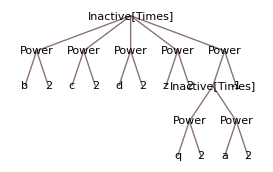

```mathematica
TreeForm[output2]
```

```mathematica
ExpressionTree[output2]
```

-Graphics-

```mathematica
Head[b^2×c^2×d^2×z^2×1/(q^2×a^2)]
```

Inactive[Times]

```mathematica
Replace[b^2×c^2×d^2×z^2×1/(q^2×a^2),Inactive[Times][OrderlessPatternSequence[numerator:RepeatedNull[x_/;Head[x]!=Inactive[Times]],___]]:>(<|"numerator"->{numerator}|>)]
```

<|numerator→{}|>

```mathematica
MatchQ[Inactive[Times][b^2, c^2, d^2, z^2, Inactive[Times][q^2, a^2]^
  (-1)],Inactive[Times][___]]
```

True

```mathematica
MatchQ[Inactive[Times][b^2, c^2, d^2, z^2, Inactive[Times][q^2, a^2]^
  (-1)],Inactive[Times][___,___]]
```

Head::argt: Head called with 0 arguments; 1 or 2 arguments are expected.

Head::argt: Head called with 3 arguments; 1 or 2 arguments are expected.

Head::argt: Head called with 4 arguments; 1 or 2 arguments are expected.

Head::argt: Head called with 5 arguments; 1 or 2 arguments are expected.

False

```mathematica
MatchQ[b^2,x_/;Head[x]!=Inactive[Times]]
```

False

```mathematica
MatchQ[b^2,x_/;Head[x]=!=Inactive[Times]]
```

True

```mathematica
MatchQ[b^2,x_/;Head[x]=!=Inactive[Times]]
```

True

```mathematica
MatchQ[1/(q^2×a^2),x_/;Head[x]=!=Inactive[Times]]
```

True

```mathematica
Head[1/(q^2×a^2)]
```

Power

```mathematica
Cases[1/(q^2×a^2),Inactive[Times],All,Heads->True]
```

{Inactive[Times]}

```mathematica
MemberQ[Cases[1/(q^2×a^2),Inactive[Times],All,Heads->True],Inactive[Times]]
```

True

```mathematica
Cases[b^2,Inactive[Times],All,Heads->True]
```

{}

```mathematica
MemberQ[Cases[b^2,Inactive[Times],All,Heads->True],Inactive[Times]]
```

False

```mathematica
InputForm[1/(q^2×a^2)]
```

Inactive[Times][q^2, a^2]^(-1)

```mathematica
MatchQ[b^2×c^2×d^2×z^2,Inactive[Times][numerator:Repeated[x_/;!MemberQ[Cases[x,Inactive[Times],All,Heads->True],Inactive[Times]]]]]
```

False

```mathematica
MatchQ[b^2×c^2×d^2×z^2,Inactive[Times][numerator:Repeated[x_]]]
```

False

```mathematica
Replace[b^2×c^2×d^2×z^2×1/(q^2×a^2),Inactive[Times][OrderlessPatternSequence[numerator:Repeated[x_/;!MemberQ[Cases[x,Inactive[Times],All,Heads->True],Inactive[Times]]],denominator:Repeated[x_/;MemberQ[Cases[x,Inactive[Times],All,Heads->True],Inactive[Times]]]]]:>(<|"denominator"->{denominator}|>)]
```

b^2×c^2×d^2×z^2×1/(q^2×a^2)

```mathematica
SetAttributes[RearrangeFunction2,{HoldFirst,Listable}]
RearrangeFunction2[input_]:=
Module[{firstoutput},
firstoutput=Inactivate[input,Times]//. {Inactive[Times][i:(_?AtomQ..)]
:>NonCommutativeMultiply@@PositionQInFrontOfList[{i}],Inactive[Times][OrderlessPatternSequence[
n:((_^_?(#1>0&)|_?(Denominator[#1]===1&))..),d:((_^_?(#1<0&)|_?(Denominator[#1]=!=1&))..)]]:>
(NonCommutativeMultiply@@PositionQInFrontOfList[{n}]/.
 NonCommutativeMultiply[x_]:>x)/
 (NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{d}]/. NonCommutativeMultiply[y_]:>y),
 
NonCommutativeMultiply[i:(_?NumericQ..)]:>Times[i],u:NonCommutativeMultiply[___]/;Cases[u,q|q^_]!={}:>
NonCommutativeMultiply@@PositionQInFrontOfList[List@@u],Inactive[Times][y__]:>NonCommutativeMultiply[y]}/. 
Inactive[Times][i:(_?NumericQ..)]:>Times[i];Replace[Replace[DeleteCases[firstoutput/. 
OrderlessPatternSequence[numbers:(_?NumericQ..),symbols:(_Symbol...),powers:(_^_...)]
**(plus:((+__)...)):>Times@@numbers NonCommutativeMultiply@@PositionQInFrontOfList[Join[{symbols},{powers},{plus}]],
NonCommutativeMultiply[],All],NonCommutativeMultiply[x_]:>x,All],{NonCommutativeMultiply[nonqs:Repeated[_?(Head[#]==
Symbol&&#=!=q&)],qs:Power[NonCommutativeMultiply[q,_],_]]:>NonCommutativeMultiply[qs,nonqs]},All]]
```

```mathematica
RearrangeFunction2[((b c d z)/(q a))^2]
```

(b**c**d**z)^2/(q**a)^2

```mathematica
Inactivate[((b c d z)/(q a))^2,Times]
```

((b×c×d×z)×1/(q×a))^2

```mathematica
(Inactivate[((b c d z)/(q a))^2,Times]//.{EchoEvaluation[Inactive[Times][i:(_?AtomQ..)]
:>Inactive[Times]@@PositionQInFrontOfList[{i}]]}),{Inactive[Times][OrderlessPatternSequence[
n:((_^_?(#1>0&)|_?(Denominator[#1]===1&))..),d:((_^_?(#1<0&)|_?(Denominator[#1]=!=1&))..)]]:>
(NonCommutativeMultiply@@PositionQInFrontOfList[{n}]/.
 NonCommutativeMultiply[x_]:>x)/
 (NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{d}]/. NonCommutativeMultiply[y_]:>y),
 
NonCommutativeMultiply[i:(_?NumericQ..)]:>Times[i],u:NonCommutativeMultiply[___]/;Cases[u,q|q^_]!={}:>
NonCommutativeMultiply@@PositionQInFrontOfList[List@@u],Inactive[Times][y__]:>NonCommutativeMultiply[y]}
```

Inactive[Times][i:(_?AtomQ..)]:>Inactive[Times]@@PositionQInFrontOfList[{i}]

Inactive[Times][i:(_?AtomQ..)]:>Inactive[Times]@@PositionQInFrontOfList[{i}]

(b×c×d×z)^2/(q×a)^2

```mathematica
SetAttributes[RearrangeFunction2,{HoldFirst,Listable}]
RearrangeFunction2[input_]:=
Module[{firstoutput},firstoutput=Inactivate[input,Times]//.{Inactive[Times][i:(_?AtomQ..)]:>NonCommutativeMultiply@@PositionQInFrontOfList[{i}],Inactive[Times][OrderlessPatternSequence[n:((_^_?(#1>0&)|_?(NumeratorTermQ[#1]&))..),d:((_^_?(#1<0&)|_?(DenominatorTermQ[#1]&))..)]]:>(NonCommutativeMultiply@@PositionQInFrontOfList[{n}]/.
NonCommutativeMultiply[x_]:>x)/(NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{d}]/. NonCommutativeMultiply[y_]:>y),NonCommutativeMultiply[i:(_?NumericQ..)]:>Times[i],u:NonCommutativeMultiply[___]/;Cases[u,q|q^_]!={}:>NonCommutativeMultiply@@PositionQInFrontOfList[List@@u],Inactive[Times][y__]:>NonCommutativeMultiply[y]}/. Inactive[Times][i:(_?NumericQ..)]:>Times[i];
Replace[Replace[DeleteCases[firstoutput/. OrderlessPatternSequence[numbers:(_?NumericQ..),symbols:(_Symbol...),powers:(_^_...)]**(plus:((+__)...)):>Times@@numbers NonCommutativeMultiply@@PositionQInFrontOfList[Join[{symbols},{powers},{plus}]],NonCommutativeMultiply[],All],NonCommutativeMultiply[x_]:>x,All],{NonCommutativeMultiply[nonqs:Repeated[_?(Head[#]==Symbol&&#=!=q&)],qs:Power[NonCommutativeMultiply[q,_],_]]:>NonCommutativeMultiply[qs,nonqs]},All]]
```

```mathematica
RearrangeFunction2[a b c d ]
```

a**b**c**d

```mathematica
RearrangeFunction2[a b c d q]
```

q**a**b**c**d

```mathematica
RearrangeFunction2[a b c d q^n]
```

q^n**a**b**c**d

```mathematica
RearrangeFunction2[a b c d q^(n-1)]
```

q^(-1+n)**a**b**c**d

```mathematica
Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][i:(_?AtomQ..)]:>NonCommutativeMultiply@@PositionQInFrontOfList[{i}],Inactive[Times][OrderlessPatternSequence[n:((_^_?(#1>0&)|_?(Denominator[#1]===1&))..),d:((_^_?(#1<0&)|_?(Denominator[#1]=!=1&))..)]]:>(NonCommutativeMultiply@@PositionQInFrontOfList[{n}]/.
NonCommutativeMultiply[x_]:>x)/(NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{d}]/. NonCommutativeMultiply[y_]:>y),NonCommutativeMultiply[i:(_?NumericQ..)]:>Times[i],u:NonCommutativeMultiply[___]/;Cases[u,q|q^_]!={}:>NonCommutativeMultiply@@PositionQInFrontOfList[List@@u],Inactive[Times][y__]:>NonCommutativeMultiply[y]}/. Inactive[Times][i:(_?NumericQ..)]:>Times[i]
```

(a**b**c**d)/q

```mathematica
Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][OrderlessPatternSequence[n:((_^_?(#1>0&)|_?(Denominator[#1]===1&))..),d:((_^_?(#1<0&)|_?(Denominator[#1]=!=1&))..)]]:>{{n},{d}}}
```

{{a,b,c,d},{q^(-1+n)}}

```mathematica
Inactivate[a b c d q^(n-1),Times]
```

a×b×c×d×q^(-1+n)

```mathematica
MatchQ[q^(-1+n),TrueQ[_^(_?(#1<0&))]]
```

False

```mathematica
MatchQ[q^(-1+n),_?(Denominator[#1]=!=1&)]
```

True

```mathematica
CloudGet["https://www.wolframcloud.com/obj/burbery1/cloudfunctions/NumeratorTermQ"]
```

```mathematica
NumeratorTermQ[q^(-1+n)]
```

True

```mathematica
Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][OrderlessPatternSequence[n:((_^_?(#1>0&)|_?(NumeratorTermQ[#1]&))..),d:((_^_?(#1<0&)|_?(DenominatorTermQ[#1]&))..)]]:>{{n},{d}}}
```

a×b×c×d×q^(-1+n)

```mathematica
RearrangeFunction2[a b c d q^(n-1)]
```

q^(-1+n)**a**b**c**d

```mathematica
RearrangeMultiplicativeSubExpressions[a b c d q^(n-1)]
```

(a**b**c**d)/q

```mathematica
Module[{firstoutput}, 
 firstoutput = 
  Inactivate[a b c d q^(n-1), 
     Times] //. {Inactive[Times][i : (_?AtomQ ..)] :> 
      NonCommutativeMultiply @@ PositionQInFrontOfList[{i}], 
     Inactive[Times][
       OrderlessPatternSequence[
        n : ((_^_?(#1 > 0 &) | _?(NumeratorTermQ[#1] &)) ..), 
        d : ((_^_?(#1 < 
                  0 &) | _?(DenominatorTermQ[#1] &)) ..)]] :> \
(NonCommutativeMultiply @@ PositionQInFrontOfList[{n}] /.
         
         NonCommutativeMultiply[x_] :> x)/(NonCommutativeMultiply @@ 
          PositionQInFrontOfList[Denominator /@ {d}] /. 
         NonCommutativeMultiply[y_] :> y), 
     NonCommutativeMultiply[i : (_?NumericQ ..)] :> Times[i], 
     u : NonCommutativeMultiply[___] /; Cases[u, q | q^_] != {} :> 
      NonCommutativeMultiply @@ PositionQInFrontOfList[List @@ u], 
     Inactive[Times][y__] :> NonCommutativeMultiply[y]} /. 
   Inactive[Times][i : (_?NumericQ ..)] :> Times[i];
 Replace[
  Replace[DeleteCases[
    firstoutput /. 
     OrderlessPatternSequence[numbers : (_?NumericQ ..), 
        symbols : (_Symbol ...), 
        powers : (_^_. ..)] ** (plus : ((+__) ...)) :> 
      Times @@ numbers NonCommutativeMultiply @@ 
        PositionQInFrontOfList[Join[{symbols}, {powers}, {plus}]], 
    NonCommutativeMultiply[], All], NonCommutativeMultiply[x_] :> x, 
   All], {NonCommutativeMultiply[
     nonqs : Repeated[_?(Head[#] == Symbol && # =!= q &)], 
     qs : Power[NonCommutativeMultiply[q, _], _]] :> 
    NonCommutativeMultiply[qs, nonqs]}, All]]
```

q^(-1+n)**a**b**c**d

```mathematica
Module[{PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput},PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput=Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?AtomQ..)]:>NonCommutativeMultiply@@PositionQInFrontOfList[{PeterBurbery`BasicHypergeometricFunctions`Private`i}],Inactive[Times][OrderlessPatternSequence[PeterBurbery`BasicHypergeometricFunctions`Private`n:((_^(_?(#1>0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`NumeratorTermQ[#1]&))..),PeterBurbery`BasicHypergeometricFunctions`Private`d:((_^(_?(#1<0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`DenominatorTermQ[#1]&))..)]]:>(NonCommutativeMultiply@@PositionQInFrontOfList[{PeterBurbery`BasicHypergeometricFunctions`Private`n}]/.NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`x_]:>PeterBurbery`BasicHypergeometricFunctions`Private`x)/(NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{PeterBurbery`BasicHypergeometricFunctions`Private`d}]/.NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`y_]:>PeterBurbery`BasicHypergeometricFunctions`Private`y),NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?NumericQ..)]:>Times[PeterBurbery`BasicHypergeometricFunctions`Private`i],PeterBurbery`BasicHypergeometricFunctions`Private`u:NonCommutativeMultiply[___]/;Cases[PeterBurbery`BasicHypergeometricFunctions`Private`u,PeterBurbery`BasicHypergeometricFunctions`Private`q|(PeterBurbery`BasicHypergeometricFunctions`Private`q)^_]≠{}:>NonCommutativeMultiply@@PositionQInFrontOfList[List@@PeterBurbery`BasicHypergeometricFunctions`Private`u],Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`y__]:>NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`y]}/.Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?NumericQ..)]:>Times[PeterBurbery`BasicHypergeometricFunctions`Private`i];Replace[Replace[DeleteCases[PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput/.OrderlessPatternSequence[PeterBurbery`BasicHypergeometricFunctions`Private`numbers:(_?NumericQ..),PeterBurbery`BasicHypergeometricFunctions`Private`symbols:(_Symbol...),PeterBurbery`BasicHypergeometricFunctions`Private`powers:(_^(_.)..)]**(PeterBurbery`BasicHypergeometricFunctions`Private`plus:((+__)...)):>Times@@PeterBurbery`BasicHypergeometricFunctions`Private`numbers NonCommutativeMultiply@@PositionQInFrontOfList[Join[{PeterBurbery`BasicHypergeometricFunctions`Private`symbols},{PeterBurbery`BasicHypergeometricFunctions`Private`powers},{PeterBurbery`BasicHypergeometricFunctions`Private`plus}]],NonCommutativeMultiply[],All],NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`x_]:>PeterBurbery`BasicHypergeometricFunctions`Private`x,All],{(PeterBurbery`BasicHypergeometricFunctions`Private`nonqs:(_?(Head[#1]==Symbol&&#1=!=PeterBurbery`BasicHypergeometricFunctions`Private`q&)..))**(PeterBurbery`BasicHypergeometricFunctions`Private`qs:(PeterBurbery`BasicHypergeometricFunctions`Private`q**_)^_):>PeterBurbery`BasicHypergeometricFunctions`Private`qs**PeterBurbery`BasicHypergeometricFunctions`Private`nonqs},All]]
```

a**b**c**d**q^(-1+n)

```mathematica
Module[{PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput},PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput=Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?AtomQ..)]:>NonCommutativeMultiply@@PositionQInFrontOfList[{PeterBurbery`BasicHypergeometricFunctions`Private`i}],Inactive[Times][OrderlessPatternSequence[n:((_^(_?(#1>0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`NumeratorTermQ[#1]&))..),d:((_^(_?(#1<0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`DenominatorTermQ[#1]&))..)]]:>(NonCommutativeMultiply@@PositionQInFrontOfList[{n}]/.NonCommutativeMultiply[x_]:>x)/(NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{d}]/.NonCommutativeMultiply[y_]:>y),NonCommutativeMultiply[i:(_?NumericQ..)]:>Times[i],u:NonCommutativeMultiply[___]/;Cases[u,q|q^_]≠{}:>NonCommutativeMultiply@@PositionQInFrontOfList[List@@u],Inactive[Times][y__]:>NonCommutativeMultiply[y]}/.Inactive[Times][i:(_?NumericQ..)]:>Times[i];Replace[Replace[DeleteCases[PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput/.OrderlessPatternSequence[numbers:(_?NumericQ..),symbols:(_Symbol...),powers:(_^(_.)..)]**(plus:((+__)...)):>Times@@numbers NonCommutativeMultiply@@PositionQInFrontOfList[Join[{symbols},{powers},{plus}]],NonCommutativeMultiply[],All],NonCommutativeMultiply[x_]:>x,All],{(nonqs:(_?(Head[#1]==Symbol&&#1=!=q&)..))**(qs:(q**_)^_):>qs**nonqs},All]]
```

q^(-1+n)**a**b**c**d

```mathematica
Block[{a,b,c,d,q,n},Module[{PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput},PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput=Inactivate[a b c d q^(n-1),Times]//.{Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?AtomQ..)]:>NonCommutativeMultiply@@PositionQInFrontOfList[{PeterBurbery`BasicHypergeometricFunctions`Private`i}],Inactive[Times][OrderlessPatternSequence[PeterBurbery`BasicHypergeometricFunctions`Private`n:((_^(_?(#1>0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`NumeratorTermQ[#1]&))..),PeterBurbery`BasicHypergeometricFunctions`Private`d:((_^(_?(#1<0&))|_?(PeterBurbery`BasicHypergeometricFunctions`Private`DenominatorTermQ[#1]&))..)]]:>(NonCommutativeMultiply@@PositionQInFrontOfList[{PeterBurbery`BasicHypergeometricFunctions`Private`n}]/.NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`x_]:>PeterBurbery`BasicHypergeometricFunctions`Private`x)/(NonCommutativeMultiply@@PositionQInFrontOfList[Denominator/@{PeterBurbery`BasicHypergeometricFunctions`Private`d}]/.NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`y_]:>PeterBurbery`BasicHypergeometricFunctions`Private`y),NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?NumericQ..)]:>Times[PeterBurbery`BasicHypergeometricFunctions`Private`i],PeterBurbery`BasicHypergeometricFunctions`Private`u:NonCommutativeMultiply[___]/;Cases[PeterBurbery`BasicHypergeometricFunctions`Private`u,PeterBurbery`BasicHypergeometricFunctions`Private`q|(PeterBurbery`BasicHypergeometricFunctions`Private`q)^_]≠{}:>NonCommutativeMultiply@@PositionQInFrontOfList[List@@PeterBurbery`BasicHypergeometricFunctions`Private`u],Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`y__]:>NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`y]}/.Inactive[Times][PeterBurbery`BasicHypergeometricFunctions`Private`i:(_?NumericQ..)]:>Times[PeterBurbery`BasicHypergeometricFunctions`Private`i];Replace[Replace[DeleteCases[PeterBurbery`BasicHypergeometricFunctions`Private`firstoutput/.OrderlessPatternSequence[PeterBurbery`BasicHypergeometricFunctions`Private`numbers:(_?NumericQ..),PeterBurbery`BasicHypergeometricFunctions`Private`symbols:(_Symbol...),PeterBurbery`BasicHypergeometricFunctions`Private`powers:(_^(_.)..)]**(PeterBurbery`BasicHypergeometricFunctions`Private`plus:((+__)...)):>Times@@PeterBurbery`BasicHypergeometricFunctions`Private`numbers NonCommutativeMultiply@@PositionQInFrontOfList[Join[{PeterBurbery`BasicHypergeometricFunctions`Private`symbols},{PeterBurbery`BasicHypergeometricFunctions`Private`powers},{PeterBurbery`BasicHypergeometricFunctions`Private`plus}]],NonCommutativeMultiply[],All],NonCommutativeMultiply[PeterBurbery`BasicHypergeometricFunctions`Private`x_]:>PeterBurbery`BasicHypergeometricFunctions`Private`x,All],{(PeterBurbery`BasicHypergeometricFunctions`Private`nonqs:(_?(Head[#1]==Symbol&&#1=!=PeterBurbery`BasicHypergeometricFunctions`Private`q&)..))**(PeterBurbery`BasicHypergeometricFunctions`Private`qs:(PeterBurbery`BasicHypergeometricFunctions`Private`q**_)^_):>PeterBurbery`BasicHypergeometricFunctions`Private`qs**PeterBurbery`BasicHypergeometricFunctions`Private`nonqs},All]]]
```

a**b**c**d**q^(-1+n)

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/BasicHypergeometricFunctions

PeterBurbery`BasicHypergeometricFunctions`

PeterBurbery/BasicHypergeometricFunctions/tutorial/RearrangingExpressions

### Keywords